```mathematica
(* Leading order perturbed solution near the corner singularity *)
```

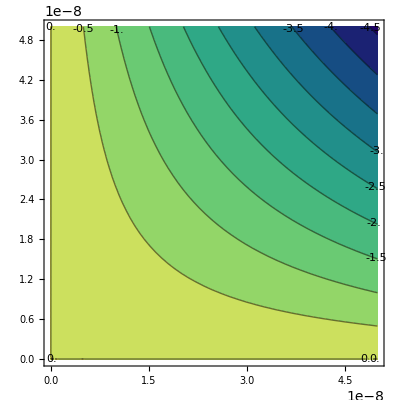

```mathematica
With[
{ϵ=5*10^(-4),ϵ0=8.85*10^(-12),R=10^(-7),q=1.6*10^(-19),M=20},
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}],{x,-ϵ R,R/2},{y,-ϵ R,R/2},ColorFunction->"BlueGreenYellow",ContourLabels->All
]
]
```

```mathematica
(* Series perturbation *)
```

```mathematica
Series[((Cos[θ]+Sin[θ])^m-Cos[m θ]-Tan[m π/(4+2ϵ)]Sin[m θ])/.{θ->R ϵr/n/r},{n,Infinity,1}]
```

(m R ϵr-m R ϵr Tan[(m π)/(4+2 ϵ)])/(r n)+O[1/n]^2

```mathematica
Series[(Cm Cos[m θ]+Dm Sin[m θ])/.{θ->R  ϵr/n/r},{n,Infinity,1}]
```

Cm+(Dm m R ϵr)/(r n)+O[1/n]^2

```mathematica
Series[((Cos[θ]+Sin[θ])^m-Cos[m θ]-Tan[m π/(4+2ϵ)]Sin[m θ])/.{θ->π/2-R ϵr/n/r},{n,Infinity,1}]
```

(1-Cos[(m π)/2]-Sin[(m π)/2] Tan[(m π)/(4+2 ϵ)])+(m R ϵr-m R ϵr Sin[(m π)/2]+m R ϵr Cos[(m π)/2] Tan[(m π)/(4+2 ϵ)])/(r n)+O[1/n]^2

```mathematica
Manipulate[
Limit[1-Cos[(m π)/2]-Sin[(m π)/2] Tan[(m π)/(4+2 ϵ)],{m->m1,ϵ->0}],{m1,1,10,1}
]
```

```mathematica
FullSimplify[(m R ϵr-m R ϵr Sin[(m π)/2]+m R ϵr Cos[(m π)/2] Tan[(m π)/(4+2 ϵ)])/(r n)]
```

(m R ϵr (1-Sin[(m π)/2]+Cos[(m π)/2] Tan[(m π)/(4+2 ϵ)]))/(n r)

```mathematica
Manipulate[
Limit[1-Sin[(m π)/(2+ϵ)]+Cos[(m π)/(2+ϵ)] Tan[(m π)/(4+2 ϵ)],{m->m1,ϵ->0}],{m1,1,10,1}
]
```

```mathematica
Series[(Cm Cos[m θ]+Dm Sin[m θ])/.{θ->π/2-R ϵr/n/r},{n,Infinity,1}]
```

(Cm Cos[(m π)/2]+Dm Sin[(m π)/2])+(-Dm m R ϵr Cos[(m π)/2]+Cm m R ϵr Sin[(m π)/2])/(r n)+O[1/n]^2

```mathematica
FullSimplify[Solve[Cos[m π/2]==0,m]]
```

{{m→ConditionalExpression[-1+4 C[1],C[1]∈ℤ]},{m→ConditionalExpression[1+4 C[1],C[1]∈ℤ]}}

```mathematica
FullSimplify[Solve[Sin[m π/2]==0,m]]
```

{{m→ConditionalExpression[4 C[1],C[1]∈ℤ]},{m→ConditionalExpression[2+4 C[1],C[1]∈ℤ]}}

```mathematica
FullSimplify[Solve[Cos[m π/4]==0,m]]
```

{{m→ConditionalExpression[-2+8 C[1],C[1]∈ℤ]},{m→ConditionalExpression[2+8 C[1],C[1]∈ℤ]}}

```mathematica
FullSimplify[Solve[Sin[m π/4]==0,m]]
```

{{m→ConditionalExpression[8 C[1],C[1]∈ℤ]},{m→ConditionalExpression[4+8 C[1],C[1]∈ℤ]}}

```mathematica
N[Table[Sin[m(π/4+ArcSin[1/Sqrt[5]])],{m,1,10,1}]]
```

{0.948683,0.6,-0.56921,-0.96,-0.0379473,0.936,0.629926,-0.5376,-0.969934,-0.07584}

```mathematica
N[(Sqrt[2]-1)Log[2]]
```

0.287111

```mathematica
Mod[210,8]
```

2

```mathematica
(* First order perturbation *)
```

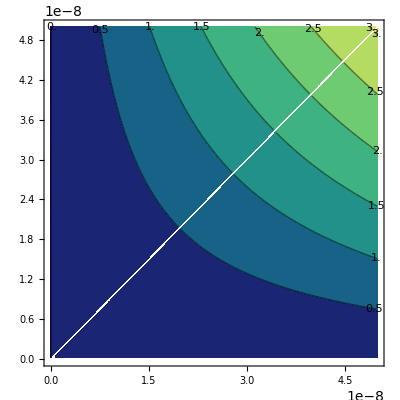

```mathematica
With[
{ϵ=7.5*10^(-4),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]
,{x,-ϵ R,R/2},{y,-ϵ R,R/2},ColorFunction->"BlueGreenYellow",ContourLabels->All
]
]
```

```mathematica
(* Matching asymptotics with near the charge fields *)
```

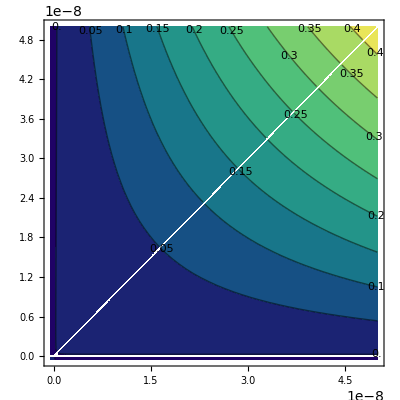

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,-ϵ R,R/2},{y,-ϵ R,R/2},ColorFunction->"BlueGreenYellow",ContourLabels->All
]
]
```

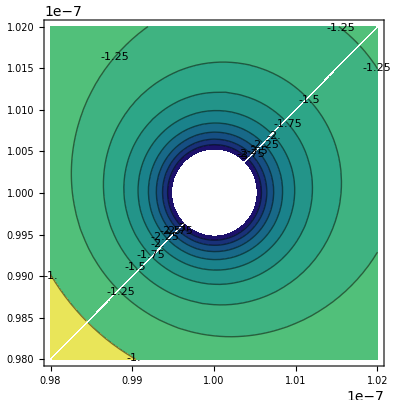

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,0.98R,1.02 R},{y,0.98R,1.02 R},ColorFunction->"BlueGreenYellow",ContourLabels->All
]
]
```

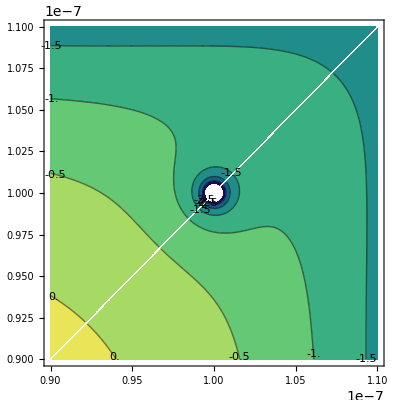

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,0.90R,1.10R},{y,0.90R,1.10R},ColorFunction->"BlueGreenYellow",ContourLabels->All
]
]
```

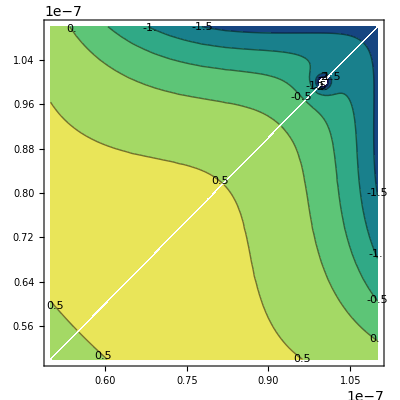

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,0.50R,1.10R},{y,0.50R,1.10R},ColorFunction->"BlueGreenYellow",ContourLabels->All
]
]
```

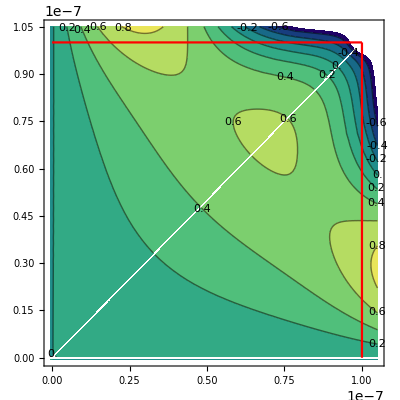

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
Show[
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,-ϵ R,1.05R},{y,-ϵ R,1.05R},ColorFunction->"BlueGreenYellow",ContourLabels->All
],
ParametricPlot[{R,x},{x,0,R},PlotStyle->Red],ParametricPlot[{x,R},{x,0,R},PlotStyle->Red]
]
]
```

```mathematica
(* The intersection of red lines is at the point charge .... *)
```

```mathematica
(* Some essential components of the calculation of the electric field *)
```

```mathematica
FullSimplify[D[-Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),x]]
```

1/((x+y) (x^2+y^2))4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) Sec[(m π)/(4+2 ϵ)] (x Cos[(m π)/(4+2 ϵ)-m ArcTan[x,y]]-y Sin[(m π)/(4+2 ϵ)-m ArcTan[x,y]]))

```mathematica
FullSimplify[D[-(1-Sqrt[x^2+y^2]/R)^n(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]] ,x]]
```

-((((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (x (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]]))/((x^2+y^2) (-R+√(x^2+y^2))))

```mathematica
FullSimplify[D[-(Sqrt[x^2+y^2]/4/R)^m,x]]
```

-(4^-m m x ((√(x^2+y^2))/R)^m)/(x^2+y^2)

```mathematica
Simplify[D[-(-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)((Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]))),x]]
```

-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (-m y (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)])

```mathematica
FullSimplify[D[-Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),y]]
```

1/((x+y) (x^2+y^2))4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) (y Cos[m ArcTan[x,y]]-x Sin[m ArcTan[x,y]]+(x Cos[m ArcTan[x,y]]+y Sin[m ArcTan[x,y]]) Tan[(m π)/(4+2 ϵ)]))

```mathematica
FullSimplify[D[-(1-Sqrt[x^2+y^2]/R)^n(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]] ,y]]
```

1/((x^2+y^2) (-R+√(x^2+y^2)))((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (-y (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m x (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])

```mathematica
Simplify[D[-(-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)((Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]))),y]]
```

-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m x (R-√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (m x (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)])

```mathematica
FullSimplify[D[-(Sqrt[x^2+y^2]/4/R)^m,y]]
```

-(4^-m m y ((√(x^2+y^2))/R)^m)/(x^2+y^2)

```mathematica
FullSimplify[D[-q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2]),x]]
```

(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)

```mathematica
FullSimplify[D[-q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2]),y]]
```

(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)

```mathematica
(* Electric field lines and electric potential plotted together *)
```

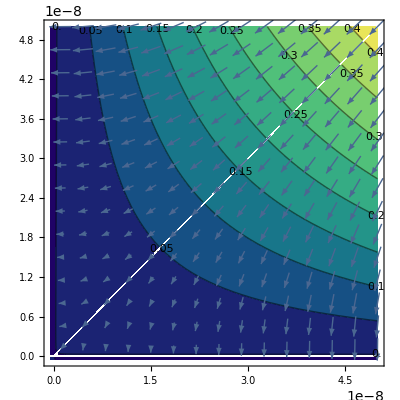

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
Show[
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]
+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,-ϵ R,R/2},{y,-ϵ R,R/2},ColorFunction->"BlueGreenYellow",ContourLabels->All
],
VectorPlot[{(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+q/(4 Sqrt[2]π ϵ0 R)Sum[4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) Sec[(m π)/(4+2 ϵ)] (x Cos[(m π)/(4+2 ϵ)-m ArcTan[x,y]]-y Sin[(m π)/(4+2 ϵ)-m ArcTan[x,y]]))/((x+y) (x^2+y^2)),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(1/((x^2+y^2) (-R+√(x^2+y^2)))((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (-y (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m x (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m x ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (-m y (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]],
q/(4 Sqrt[2]π ϵ0 R)Sum[1/((x+y) (x^2+y^2))4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) (y Cos[m ArcTan[x,y]]-x Sin[m ArcTan[x,y]]+(x Cos[m ArcTan[x,y]]+y Sin[m ArcTan[x,y]]) Tan[(m π)/(4+2 ϵ)])),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(-((((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (x (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]]))/((x^2+y^2) (-R+√(x^2+y^2))))),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m y ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m x (R-√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (m x (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]]+(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)
},{x,0.01 R,R/2},{y,0.01 R,R/2},VectorScale->{0.05,1,Automatic},PlotTheme->Automatic]
]
]
```

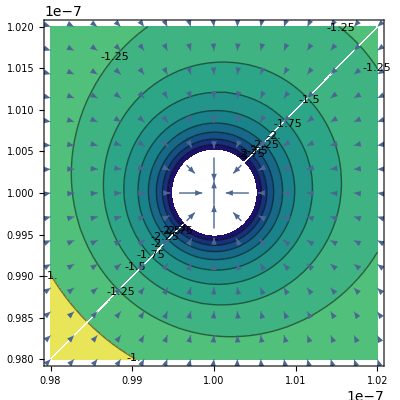

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
Show[
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]
+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,0.98R,1.02R},{y,0.98R,1.02R},ColorFunction->"BlueGreenYellow",ContourLabels->All
],
VectorPlot[{(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+q/(4 Sqrt[2]π ϵ0 R)Sum[4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) Sec[(m π)/(4+2 ϵ)] (x Cos[(m π)/(4+2 ϵ)-m ArcTan[x,y]]-y Sin[(m π)/(4+2 ϵ)-m ArcTan[x,y]]))/((x+y) (x^2+y^2)),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(1/((x^2+y^2) (-R+√(x^2+y^2)))((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (-y (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m x (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m x ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (-m y (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]],
q/(4 Sqrt[2]π ϵ0 R)Sum[1/((x+y) (x^2+y^2))4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) (y Cos[m ArcTan[x,y]]-x Sin[m ArcTan[x,y]]+(x Cos[m ArcTan[x,y]]+y Sin[m ArcTan[x,y]]) Tan[(m π)/(4+2 ϵ)])),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(-((((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (x (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]]))/((x^2+y^2) (-R+√(x^2+y^2))))),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m y ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m x (R-√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (m x (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]]+(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)
},{x,0.98R,1.02R},{y,0.98R,1.02R},VectorScale->{0.05,1,Automatic},PlotTheme->Automatic]
]
]
```

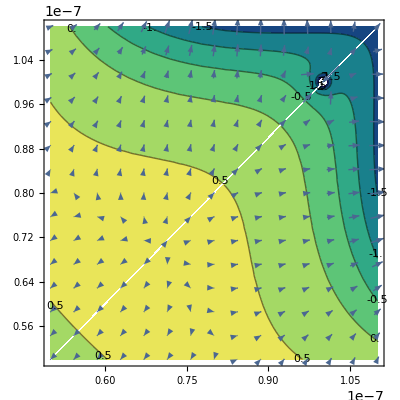

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
Show[
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]
+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,0.50R,1.10R},{y,0.50R,1.10R},ColorFunction->"BlueGreenYellow",ContourLabels->All
],
VectorPlot[{(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+q/(4 Sqrt[2]π ϵ0 R)Sum[4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) Sec[(m π)/(4+2 ϵ)] (x Cos[(m π)/(4+2 ϵ)-m ArcTan[x,y]]-y Sin[(m π)/(4+2 ϵ)-m ArcTan[x,y]]))/((x+y) (x^2+y^2)),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(1/((x^2+y^2) (-R+√(x^2+y^2)))((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (-y (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m x (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m x ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (-m y (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]],
q/(4 Sqrt[2]π ϵ0 R)Sum[1/((x+y) (x^2+y^2))4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) (y Cos[m ArcTan[x,y]]-x Sin[m ArcTan[x,y]]+(x Cos[m ArcTan[x,y]]+y Sin[m ArcTan[x,y]]) Tan[(m π)/(4+2 ϵ)])),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(-((((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (x (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]]))/((x^2+y^2) (-R+√(x^2+y^2))))),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m y ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m x (R-√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (m x (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]]+(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)
},{x,0.50R,1.10R},{y,0.50R,1.10R},VectorScale->{0.05,1,Automatic},PlotTheme->Automatic]
]
]
```

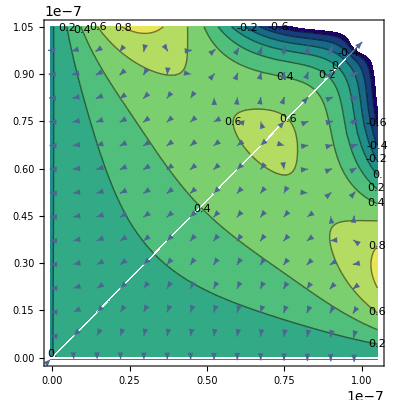

```mathematica
With[
{ϵ=5*10^(-3),ϵ0=8.85*10^(-12),R=10^(-7),q=-1.6*10^(-19),M=10,n=1000},
Show[
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]
+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,-ϵ R,1.05R},{y,-ϵ R,1.05R},ColorFunction->"BlueGreenYellow",ContourLabels->All
],
VectorPlot[{(q (-R+x))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)+q/(4 Sqrt[2]π ϵ0 R)Sum[4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) Sec[(m π)/(4+2 ϵ)] (x Cos[(m π)/(4+2 ϵ)-m ArcTan[x,y]]-y Sin[(m π)/(4+2 ϵ)-m ArcTan[x,y]]))/((x+y) (x^2+y^2)),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(1/((x^2+y^2) (-R+√(x^2+y^2)))((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (-y (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m x (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m x ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (-m y (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+x (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]],
q/(4 Sqrt[2]π ϵ0 R)Sum[1/((x+y) (x^2+y^2))4^-m m ((√(x^2+y^2))/R)^m Binomial[2 m,m] (-((x+y)/(√(x^2+y^2)))^m (x^2+y^2)+(x+y) (y Cos[m ArcTan[x,y]]-x Sin[m ArcTan[x,y]]+(x Cos[m ArcTan[x,y]]+y Sin[m ArcTan[x,y]]) Tan[(m π)/(4+2 ϵ)])),{m,1,M}]+If[0≤ArcTan[x,y]<π/4,q/(4 Sqrt[2]n π ϵ0 R)Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Tan[(m+1)π/(4+2ϵ)]-1)(-((((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n (x (n √(x^2+y^2)+m (-R+√(x^2+y^2))) Cos[m ArcTan[x,y]]+m y (-R+√(x^2+y^2)) Sin[m ArcTan[x,y]]))/((x^2+y^2) (-R+√(x^2+y^2))))),{m,1,M}],If[ArcTan[x,y]==π/4,-q Log[2]/(16 n π ϵ0 R)Sum[(-(4^-m m y ((√(x^2+y^2))/R)^m)/(x^2+y^2))Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],Sum[-1/(n π R (x^2+y^2) (-R+√(x^2+y^2)) ϵ0)2^(-9/2-2 m) (1+m) q ((√(x^2+y^2))/R)^m (1-(√(x^2+y^2))/R)^n Binomial[2+2 m,1+m] (If[Mod[m,2]==0,Sec[(m π)/2],0] (y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Cos[m ArcTan[x,y]]+m x (R-√(x^2+y^2)) Sin[m ArcTan[x,y]])+If[Mod[m,2]==1,Csc[(m π)/2],0] (m x (-R+√(x^2+y^2)) Cos[m ArcTan[x,y]]+y (-m R+m √(x^2+y^2)+n √(x^2+y^2)) Sin[m ArcTan[x,y]])) (-1+Sin[((1+m) π)/(2+ϵ)]+Cos[((1+m) π)/(2+ϵ)] Tan[((1+m) π)/(4+2 ϵ)]),{m,1,M}]]]+(q (-R+y))/(4 π ((R-x)^2+(R-y)^2)^(3/2) ϵ0)
},{x,-ϵ R,1.05R},{y,-ϵ R,1.05R},VectorScale->{0.05,1,Automatic},PlotTheme->Automatic]
]
]
```

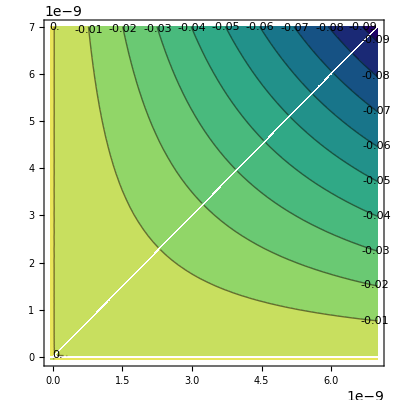

```mathematica
With[
{ϵ=5*10^(-4),ϵ0=8.85*10^(-12),R=10^(-7),q=1.6*10^(-19),M=10,n=10^8},
ContourPlot[
q/(4 Sqrt[2]π ϵ0 R)Sum[Binomial[2m,m](Sqrt[x^2+y^2]/4/R)^m(((x+y)/Sqrt[x^2+y^2])^m-Cos[m ArcTan[x,y]]-Tan[m π/(4+2 ϵ)]Sin[m ArcTan[x,y]]),{m,1,M}]+
If[
0≤ArcTan[x,y]<π/4,
q/(4 Sqrt[2]π ϵ0 R)1/n(1-Sqrt[x^2+y^2]/R)^n Sum[Binomial[2m+2,m+1](m+1)/4^(m+1)(Sqrt[x^2+y^2]/R)^m Cos[m ArcTan[x,y]](Tan[(m+1)π/(4+2ϵ)]-1),{m,1,M}],
If[
ArcTan[x,y]==π/4,
-q Log[2]/(16 n π ϵ0 R)Sum[(Sqrt[x^2+y^2]/4/R)^m Binomial[2m+2,m+1](2^((m+1)/2)-Cos[(m+1)π/4]-Sin[(m+1)π/4]Tan[(m+1) π/(4+2ϵ)]),{m,1,M}],
-1/n(1-Sqrt[x^2+y^2]/R)^n q/(4 Sqrt[2]π ϵ0 R)Sum[(Sqrt[x^2+y^2]/R)^m Binomial[2m+2,m+1](m+1)/4^(m+1)(1-Sin[(m+1)π/(2+ϵ)]-Cos[(m+1)π/(2+ϵ)]Tan[(m+1)π/(4+2ϵ)])(If[Mod[m,2]==0,Sec[m π/2],0] Cos[m ArcTan[x,y]]+If[Mod[m,2]==1,Csc[m π/2],0] Sin[m ArcTan[x,y]]),{m,1,M}]
]
]+q/(4π ϵ0 Sqrt[(x-R)^2+(y-R)^2])-q/(4Sqrt[2]π ϵ0 R)
,{x,-ϵ R,0.07R},{y,-ϵ R,0.07R},ColorFunction->"BlueGreenYellow",ContourLabels->All
]
]
```

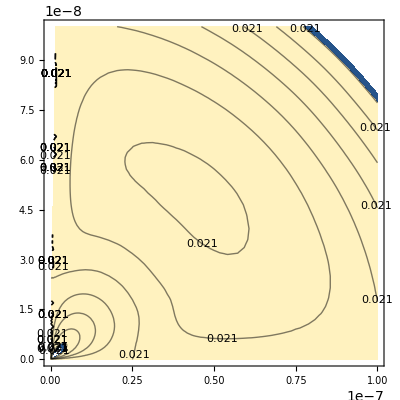

```mathematica
Block[
{potent,ϕ0,f,ϵ,ϵ0,R,q},
ϵ=2.1*10^(-2);R=10^(-7);q=-1.6*10^(-19);ϵ0=8.85*10^(-12);ϕ0=ϵ;
potent=NDSolveValue[{Laplacian[f[r,θ],{r,θ},"Polar"]==q/ϵ0/r^2 DiracDelta[r-Sqrt[2]R]DiracDelta[θ-π/4],f[r,0]==ϕ0,f[r,π/(2+ϵ)]==ϕ0},f[r,θ],{r,0,Sqrt[2]R},{θ,0,π/(2+ϵ)}];
ContourPlot[potent/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]},{x,0,R},{y,0,R},ContourLabels->All]
]
```

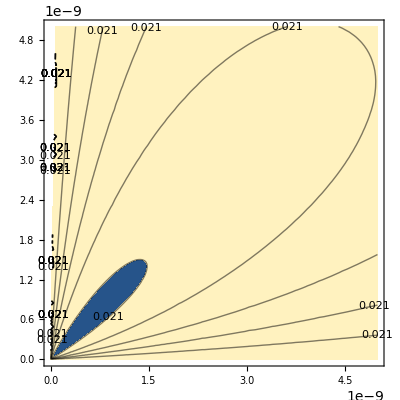

```mathematica
Block[
{potent,ϕ0,f,ϵ,ϵ0,R,q},
ϵ=2.1*10^(-2);R=10^(-7);q=-1.6*10^(-19);ϵ0=8.85*10^(-12);ϕ0=ϵ;
potent=NDSolveValue[{Laplacian[f[r,θ],{r,θ},"Polar"]==q/ϵ0/r^2 DiracDelta[r-Sqrt[2]R]DiracDelta[θ-π/4],f[r,0]==ϕ0,f[r,π/(2+ϵ)]==ϕ0},f[r,θ],{r,0,Sqrt[2]R},{θ,0,π/(2+ϵ)}];
ContourPlot[potent/.{r->Sqrt[x^2+y^2],θ->ArcTan[x,y]},{x,0,0.05R},{y,0,0.05R},ContourLabels->All]
]
```